# Autómata celular para la descripción del tráfico vehicular

## Introducción

Los autómatas celulares (AC) son un modelo interesante que nos permite describir modelos de sistemas dinámicos discretizados. Uno de los ejemplos más famosos e ilustrativos es el llamado juego de la vida de John  Conway. Este sistema muestra una dinámica compleja a partir de dos reglas simples que determinan el estado futuro de cada célula. Otro ejemplo más actual y con aplicación práctica es autómata celular elemental que se usa en el cifrado Wolfram.

En general un sistema que sea susceptible a ser discretizable, y que su evolución temporal esté definida por reglas globales que se aplican local y simultáneamente son buenos candidatos a ser estudiados mediante un modelo de AC. Un sistema de esta categoría que es interesante, es el modelado del tráfico automovilístico.

## Regla 184

Para el caso de una simulación simple del tráfico utilizando un autómata celular, se puede usar la regla 184 del autómata celular de Wolfram, la cual consiste en un arreglo unidimensional de celdas, cada una de las cuales tiene dos posibles estados 0 o 1. En cada paso de su evolución, se aplican las siguientes reglas para cada una de las células en la red, de manera simultánea para determinar el nuevo estado de la red.

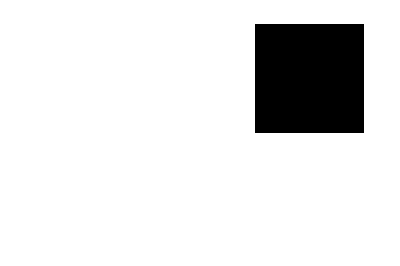
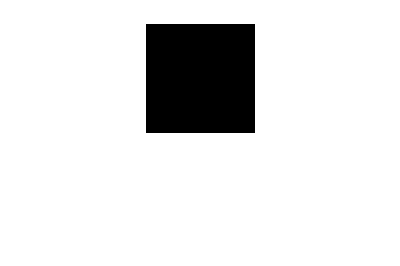
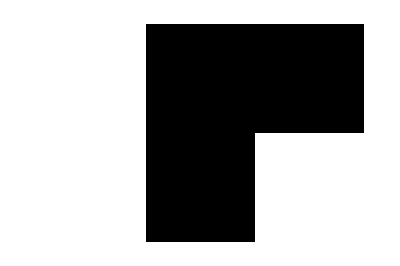
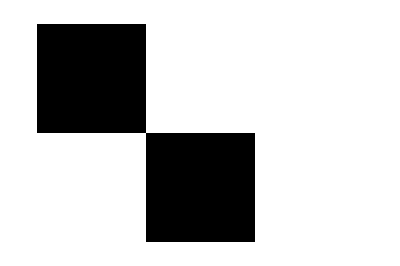
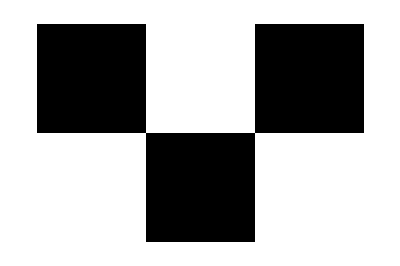
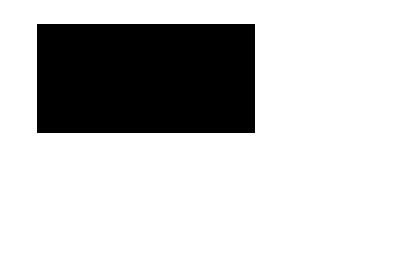
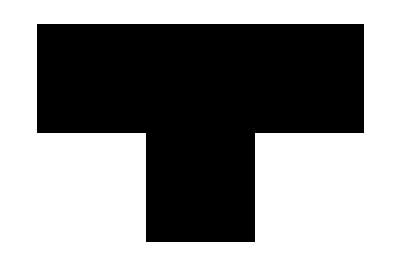
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
t = Table[CellularAutomaton[184,i,1],{i,Tuples[{0,1},3]}];
Do[t[[i]][[2]][[{1,3}]] = 0,{i,1,Length[t]}]
Table[ArrayPlot[i, ImageSize->Tiny],{i,t}]
```

La evolución del sistema es la siguiente.

```mathematica
SetOptions[ArrayPlot,BaseStyle->{FontSize->14}];
ArrayPlot[CellularAutomaton[184,RandomInteger[1,100],100],PlotLegends->Automatic,FrameTicks->Automatic,FrameLabel->{"Tiempo","Longitud"},PixelConstrained->3, PlotLabel->"Regla 184"]
```

-Graphics-

## Modelo Kai-Nagel

Un modelo más realista que nos permite simular las pequeñas variaciones de velocidad aleatorias que ocurren en el tráfico, y que además permite un mayor rango de velocidades permitidas de cada auto que pertenece al autómata celular es el propuesto por Kai Nagel y Michael Schreckenberg.

La descripción del modelo es la siguiente. Se elabora un arreglo unidimensional de longitud S, y con condiciones de frontera periódicas, lo que emula un flujo constante de autos por la autopista, uno puede ver esto como un conjunto de autos moviendo en un circuito cerrado.

Cada vehículo tiene una velocidad entera que se encuentra entre [0,vmax]. Para una configuración arbitraria, la evolución de este autómata se encuentra siguiendo los siguientes pasos, en paralelo para cada auto:

Aceleración: Si la velocidad v de un vehículo es menor que vmax y la distancia con el siguiente auto es mayor que v+1, la velocidad se aumenta en una unidad v → v+1.

Frenado: Si un vehículo en la posición i observa al siguiente vehículo en la posición i+j, reduce su velocidad a v → j-1.

Aleatorización: Con probabilidad p, la velocidad de cada vehículo (si es mayor que cero) disminuye en uno v → v-1.

Movimiento vehicular: Cada vehículo avanza v espacios.

A continuación se muestra una implementación del algoritmo.

```mathematica
(* Valores iniciales por defecto *)
EMPTY = -1;
FLOW = 1;
NOFLOW = 0;
size=20;
vmax=5;
randprob = 0.2;
density = 0.4;
positions = RandomSample[Range[size]][[1;;Round[size*density]]];
ca = Table[-1,{size}];
ca[[positions]] =1;
flow = Table[NOFLOW,{size}];
camap = {};
flowmap = {};

(* Función para reiniciar *)
Initialize[asize_, adensity_,avmax_,arandprob_] :=Module[{},
size = asize;
density=adensity;
vmax = avmax;
randprob = arandprob;

positions = RandomSample[Range[size]][[1;;Round[size*density]]];
ca = Table[-1,{size}];
ca[[positions]] =1;
flow = Table[NOFLOW,{size}];
camap = {};
flowmap = {};
]

(* Devuelve ca[[i]] con condiciones de frontera periódicas *)
At[i_] := If[i <= size,
Return[ca[[i]]],
Return[ca[[i-size]]]
]

(* Devuelve distancia a vehículo más cercano desde i hacia la derecha *)
NextCarDist[i_] := Module[{distance},
distance = 1;
While[At[i+distance] == EMPTY, distance++];
Return[distance];
]

(* Calcula cambios de las velocidades *)
Step[]:=Do[
If[ca[[i]] ≠ EMPTY,
(* Aceleración *)
If[(ca[[i]] < vmax) && (NextCarDist[i] > (ca[[i]]+1)),
ca[[i]]++;
]
(* Frenado *)
If[ca[[i]] > 0,
nd = NextCarDist[i];
If[nd ≤ ca[[i]],
ca[[i]] = nd -1;
]
]
(* Aleatoriedad *)
If[(ca[[i]] > 0) && (RandomReal[] ≤ randprob),
ca[[i]]--;
]
]
,{i,1,Length[ca]}
]

(* Realiza el movimiento de los vehículos *)
Move[]:=Module[{tmpca,i},
tmpca = Table[-1,{size}];
flow = Table[NOFLOW,{size}];
Do[
If[ca[[i]] ≠ EMPTY,
(* Actualiza posición *)
pos = i+ca[[i]];
 If[pos <= size,
tmpca[[pos]]= ca[[i]],
tmpca[[pos-size]] = ca[[i]]
]

(* Lista de flujo *)
If[ca[[i]] > 0,
Do[If[j<= size,
flow[[j]]= FLOW,
flow[[j-size]] = FLOW
],{j,i,i+ca[[i]]}
]
]
]
,{i,1,Length[ca]}
];
ca = tmpca;
]

(* Evoluciona el sistema un número dado de iteraciones *)
Evolve[iterations_] := Module[{},
Do[
Step[];
Move[];
AppendTo[camap, ca];
AppendTo[flowmap, flow];
,{iterations}
]
]

(* Función para medir el flujo de vehículos *)
MeasureFlow[] := Module[{height, width, sum},
height = Length[flowmap];
width = Length[flowmap[[1]]];
sum = 0;
Do[
Do[
If[(flowmap[[j]][[i]] ≠ NOFLOW) && (flowmap[[j]][[i+1]] ≠ NOFLOW),
sum++;
]
,{j, 1, height}
]
,{i,1, width-1}
];
Return[sum/(height*width)];
]
```

Al ejecutar la regla del autómata celular se pueden observar las ondas de tráfico que se generan.

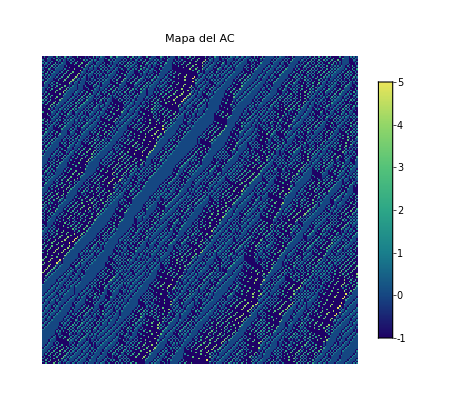

-Graphics-

```mathematica
Initialize[200, 0.5, 5, 0.2];
Evolve[200];
ArrayPlot[camap,ColorFunction->"BlueGreenYellow",FrameTicks->Automatic,PlotLegends->Automatic, PlotLabel->"Mapa del AC", FrameLabel->{"Iteración","Posición"}]

ArrayPlot[flowmap,FrameTicks->Automatic,PlotLegends->Automatic, PlotLabel->"Mapa del flujo del AC.\n"<>"Flujo: " <> ToString[N[MeasureFlow[]]], FrameLabel->{"Iteración","Posición"}]
```

Si se mide el flujo q respecto a la densidad de vehículos se observa que el sistema tiene una capacidad de carga donde ocurre la mayor cantidad de flujo, y este decae al sobrepasar la cantidad de carga del sistema.

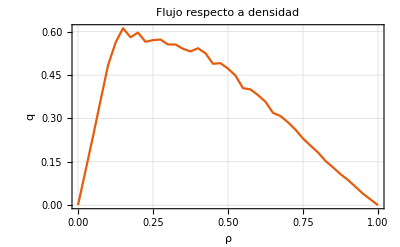

```mathematica
data={};
Do[
Initialize[200, ρ, 5, 0.2];
Evolve[200];
AppendTo[data,{ρ,MeasureFlow[]}];
,{ρ,0,1,0.025}
]
ListLinePlot[data,PlotTheme->"Scientific", FrameLabel->{"ρ", "q"}, GridLines->Automatic, PlotLabel->"Flujo respecto a densidad"]
```